# Аттестация 1 Чобану АртёмI1902

```mathematica
3.	Вычислить пределы:
```

```mathematica
Limit[(1+1/(4k))^k, k-> Infinity]
```

```mathematica
ⅇ^(1/4)
```

```mathematica
Limit[Sum[l/k^(4/7),{l,4}], k -> Infinity]
```

0

```mathematica
Limit[4/ϵ^k, k-> Infinity]
```

ConditionalExpression[0, Log[ϵ]>0]

```mathematica
4. Вычислить суммы:
```

```mathematica
Sum[4/k^4, {k, Infinity}]
```

(2 π^4)/45

```mathematica
Sum[Sin[4*k]/k^4, {k, Infinity}]
```

1/2 ⅈ (PolyLog[4,ⅇ^(-4 ⅈ)]-PolyLog[4,ⅇ^(4 ⅈ)])

```mathematica
Sum[4/Log[k], {k,2, Infinity}]
```

Sum::div: Sum does not converge.

∑_(k=2)^∞ 4/Log[k]

```mathematica
5. Вычислить произведение:
```

```mathematica
Product[k,{k,1,3*4}]
```

479001600

```mathematica
7. Вычислить производные порядка 4 для следующих ниже функций и построить графики исходных функций и производных функций ипроихводных порядка 4:
```

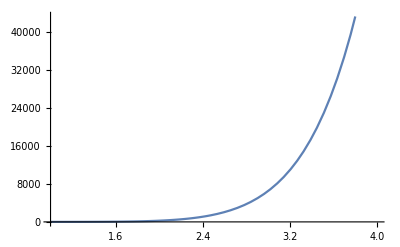

```mathematica
Plot[x^(2*4), {x,1,4}]
```

1680 x^4

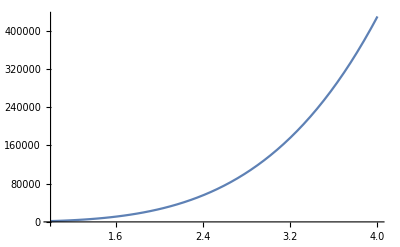

```mathematica
f[x_]:=x^8
f''''[x]
Plot[f''''[x], {x, 1, 4}]
```

```mathematica
Plot[Sin[x], {x,1,4}]
```

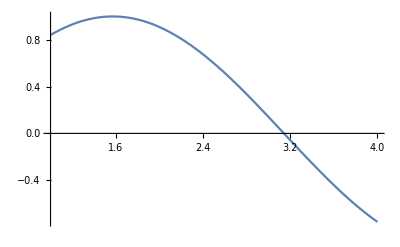

Sin[x]

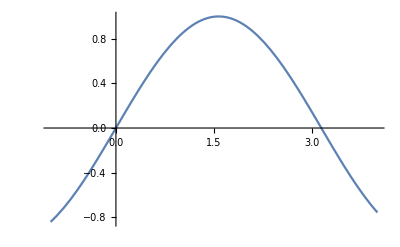

```mathematica
f[x_]:=Sin[x]
f''''[x]
Plot[f''''[x], {x, -1, 4}]
```

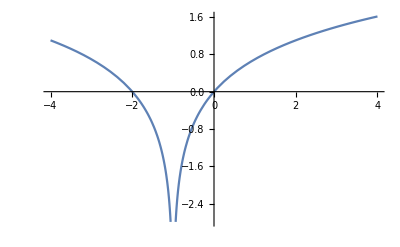

```mathematica
Plot[Log[Abs[x+1]], {x,-4,4}]
```

```mathematica
f[_x]:=Log[Abs[x+1]]
f''''[x]
Plot[f''''[x],{x,1,4}]
```

-(6 Abs'[1+x]^4)/Abs[1+x]^4+(12 Abs'[1+x]^2 Abs''[1+x])/Abs[1+x]^3-(3 Abs''[1+x]^2)/Abs[1+x]^2-(4 Abs'[1+x] Abs^(3)[1+x])/Abs[1+x]^2+(Abs^(4)[1+x])/Abs[1+x]

-Graphics-

```mathematica
8. Вычислить смешанные производные и построить графики:
```

```mathematica
D[Sin[y]*x^8, y]
```

x^8 Cos[y]

```mathematica
D[e^y*Sin[4*x^2], y]
```

e^y Log[e] Sin[4 x^2]

```mathematica
D[Log[Abs[x+y]^4], y]
```

(4 Abs'[x+y])/Abs[x+y]

```mathematica
9. Вычислить интегралы:
```

```mathematica
Integrate[x^4, x]
```

x^5/5

```mathematica
Integrate[Sin[x], {x, 4, 2*4}]
```

Cos[4]-Cos[8]

```mathematica
11. Решить системы:
```

```mathematica
Solve[{x + y == 7, x - y == -7}]
```

{{x→0,y→7}}

```mathematica
Solve[{x^4 + 4*x == 4}]
```

{{x→Root-1.84Root[-4+4 #1+#1^4&,1]-1.8350866816396352},{x→Root0.862Root[-4+4 #1+#1^4&,2]0.8619825682693073},{x→Root0.487-1.51 ⅈRoot[-4+4 #1+#1^4&,3]0.486552056685164},{x→Root0.487+1.51 ⅈRoot[-4+4 #1+#1^4&,4]0.486552056685164}}

```mathematica
Reduce[{x + 2*y >= 4, -x + y <= -4}]
```

(y≤0&&x≥4-2 y)||(y>0&&x≥4+y)

```mathematica
13. Сгенерировать список целых чисел от 1000 n до 50000 n.Вычислить сумму и произведение всех элементов тремя способами
```

```mathematica
Range[1000*4,5000*5]
```

{4000,4001,4002,4003,4004,4005,4006,4007,4008,4009,4010,4011,4012,4013,4014,4015,4016,4017,4018,4019,4020,4021,4022,4023,4024,4025,4026,4027,4028,20943,24972,24973,24974,24975,24976,24977,24978,24979,24980,24981,24982,24983,24984,24985,24986,24987,24988,24989,24990,24991,24992,24993,24994,24995,24996,24997,24998,24999,25000}
 |  |  |  |